# Cálculo de pârametros unitários de uma linha de transmissão

## Antonio Carlos S Lima EEE457 - Transmissão de Energia Elétrica 2021/1

## Início

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/acsl/Dropbox/UFRJ/cursos/EEE457-Transmissão_Energia_Elétrica/arquivos_Mma_EEE457

```mathematica
<<LineCableParam2020`
```

### Algumas constantes

```mathematica
μ= 4.0 π 10^-7;
ϵ= 8.854 10^-12;
σs=10.0^-3;
ℓ=100 10^3; (* comprimento do circuito *)
```

cabos pararraios possuem permeabilidade magnética relativa próximo a 100

```mathematica
μr= 90.0;
```

## Circuito Duplo 500kV

Coordenadas dos condutores

```mathematica
xc={-9-6,-6,-11.10,6,9+6,11.10,-6.8,6.8};
yc={27.70-4.5,27.70-4.5,27.70+10-4.5,27.70-4.5,27.70-4.5,27.70+10-4.5,27.70+10+5,27.70+10+5};
```

Dados condutores de fase

```mathematica
rf=29.59/2 10^-3;
rint=7.4/2*10^-3;
Rdc=0.06 10^-3;
```

Dados dos cabos pararraios

```mathematica
rpr=4.57*10^-3;
Rdcpr=4.19*10^-3;
```

```mathematica
mostra=Table[{Circle[{xc[[i]],yc[[i]]},{0.09,0.20}]},{i,1,Length[xc]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

-Graphics-

```mathematica
rmg1=(rf 4 Sqrt[(.457/2)^2+(.457/2)^2]^3)^(1/4)
```

0.211395

```mathematica
Prmg=Table[If[i≠j,Log[(√((xc[[i]]-xc[[j]])^2+(yc[[i]]+yc[[j]])^2))/(√((xc[[i]]-xc[[j]])^2+(yc[[i]]-yc[[j]])^2))],
If[i≤6,Log[2 yc[[i]]/rmg1],Log [2 yc[[i]]/rpr]]],{i,1,8},{j,1,8}];
```

```mathematica
PrmgInv=Inverse[Prmg];
Crmg=2 π ϵ PrmgInv[[Range[6],Range[6]]];
```

```mathematica
MatrixForm[10^12Crmg]
```

(12.1517 | -2.64627 | -2.36516 | -0.541455 | -0.207316 | -0.321821
-2.64627 | 12.6048 | -1.98019 | -1.8554 | -0.541455 | -0.731186
-2.36516 | -1.98019 | 11.9459 | -0.731186 | -0.321821 | -0.799419
-0.541455 | -1.8554 | -0.731186 | 12.6048 | -2.64627 | -1.98019
-0.207316 | -0.541455 | -0.321821 | -2.64627 | 12.1517 | -2.36516
-0.321821 | -0.731186 | -0.799419 | -1.98019 | -2.36516 | 11.9459)

```mathematica
Θx[ns_]:=Table[Cos[(1+2k) π/ns],{k,0,ns-1}]
```

```mathematica
Θy[ns_]:=Table[Sin[(1+2k) π/ns],{k,0,ns-1}]
```

```mathematica
xc1=Flatten@Join[{Flatten@Table[xc[[i]]+.457 Θx[4],{i,Length[xc]-2}],xc[[7;;8]]}];
yc1=Flatten@Join[{Flatten@Table[yc[[i]]+.457 Θy[4],{i,Length[xc]-2}],yc[[7;;8]]}];
```

```mathematica
Length[xc1]
```

26

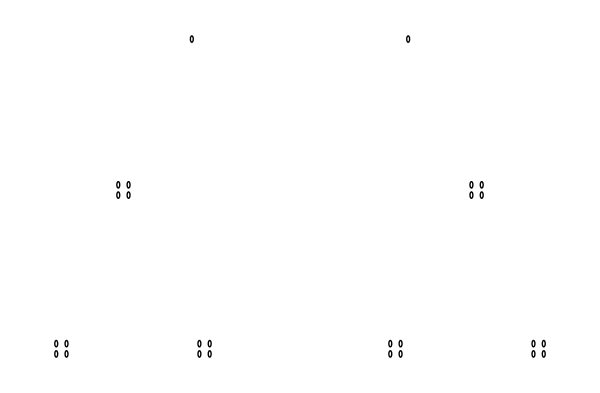

```mathematica
mostra=Table[{Circle[{xc1[[i]],yc1[[i]]},{0.09,0.20}]},{i,1,Length[xc1]}];
o1=tsimples=Show[Graphics[mostra],Axes->False,Frame->Automatic,BaseStyle->{FontFamily->"Helvetica", 14},ImageSize-> 600,FrameLabel->{Style["Distance [m]",Bold,18],Style["Distance [m]",Bold,18]}]
```

## Cálculo das matrizes

```mathematica
ω= 2. π 60;
ρs= 1000.;
npr = 2;
```

```mathematica
{Zmat, Ymat} =cZYlt[ω,xc1,yc1,1/ρs, Rdc,rf,rint, npr, Rdcpr, rpr,4];
```

```mathematica
MatrixForm[Zmat 1000]
```

(0.103508+0.665031 ⅈ | 0.0892311+0.396684 ⅈ | 0.0919668+0.380927 ⅈ | 0.0891504+0.332936 ⅈ | 0.0879956+0.307168 ⅈ | 0.0917226+0.308995 ⅈ
0.0892311+0.396684 ⅈ | 0.105756+0.662869 ⅈ | 0.0931794+0.376412 ⅈ | 0.0903502+0.373897 ⅈ | 0.0891504+0.332936 ⅈ | 0.0930478+0.3337 ⅈ
0.0919668+0.380927 ⅈ | 0.0931794+0.376412 ⅈ | 0.111733+0.657603 ⅈ | 0.0930478+0.3337 ⅈ | 0.0917226+0.308995 ⅈ | 0.0959036+0.322487 ⅈ
0.0891504+0.332936 ⅈ | 0.0903502+0.373897 ⅈ | 0.0930478+0.3337 ⅈ | 0.105756+0.662869 ⅈ | 0.0892311+0.396684 ⅈ | 0.0931794+0.376412 ⅈ
0.0879956+0.307168 ⅈ | 0.0891504+0.332936 ⅈ | 0.0917226+0.308995 ⅈ | 0.0892311+0.396684 ⅈ | 0.103508+0.665031 ⅈ | 0.0919668+0.380927 ⅈ
0.0917226+0.308995 ⅈ | 0.0930478+0.3337 ⅈ | 0.0959036+0.322487 ⅈ | 0.0931794+0.376412 ⅈ | 0.0919668+0.380927 ⅈ | 0.111733+0.657603 ⅈ)

```mathematica
MatrixForm[Ymat 1000]
```

(3.×10^-9+4.886×10^-6 ⅈ | 0.-1.11203×10^-6 ⅈ | 0.-9.89157×10^-7 ⅈ | 0.-2.14836×10^-7 ⅈ | 0.-7.95403×10^-8 ⅈ | 0.-1.25825×10^-7 ⅈ
0.-1.11203×10^-6 ⅈ | 3.×10^-9+5.08303×10^-6 ⅈ | 0.-8.23234×10^-7 ⅈ | 0.-7.77645×10^-7 ⅈ | 0.-2.14836×10^-7 ⅈ | 0.-2.95416×10^-7 ⅈ
0.-9.89157×10^-7 ⅈ | 0.-8.23234×10^-7 ⅈ | 3.×10^-9+4.7936×10^-6 ⅈ | 0.-2.95416×10^-7 ⅈ | 0.-1.25825×10^-7 ⅈ | 0.-3.29006×10^-7 ⅈ
0.-2.14836×10^-7 ⅈ | 0.-7.77645×10^-7 ⅈ | 0.-2.95416×10^-7 ⅈ | 3.×10^-9+5.08303×10^-6 ⅈ | 0.-1.11203×10^-6 ⅈ | 0.-8.23234×10^-7 ⅈ
0.-7.95403×10^-8 ⅈ | 0.-2.14836×10^-7 ⅈ | 0.-1.25825×10^-7 ⅈ | 0.-1.11203×10^-6 ⅈ | 3.×10^-9+4.886×10^-6 ⅈ | 0.-9.89157×10^-7 ⅈ
0.-1.25825×10^-7 ⅈ | 0.-2.95416×10^-7 ⅈ | 0.-3.29006×10^-7 ⅈ | 0.-8.23234×10^-7 ⅈ | 0.-9.89157×10^-7 ⅈ | 3.×10^-9+4.7936×10^-6 ⅈ)

```mathematica
Im[Ymat 1000]/( ω) -1000 Crmg
```

{{8.08832×10^-10,-3.03486×10^-10,-2.58656×10^-10,-2.84139×10^-11,-3.67072×10^-12,-1.1939×10^-11},{-3.03486×10^-10,8.78381×10^-10,-2.03505×10^-10,-2.07363×10^-10,-2.84139×10^-11,-5.24278×10^-11},{-2.58656×10^-10,-2.03505×10^-10,7.69528×10^-10,-5.24278×10^-11,-1.1939×10^-11,-7.3296×10^-11},{-2.84139×10^-11,-2.07363×10^-10,-5.24278×10^-11,8.78381×10^-10,-3.03486×10^-10,-2.03505×10^-10},{-3.67072×10^-12,-2.84139×10^-11,-1.1939×10^-11,-3.03486×10^-10,8.08832×10^-10,-2.58656×10^-10},{-1.1939×10^-11,-5.24278×10^-11,-7.3296×10^-11,-2.03505×10^-10,-2.58656×10^-10,7.69528×10^-10}}

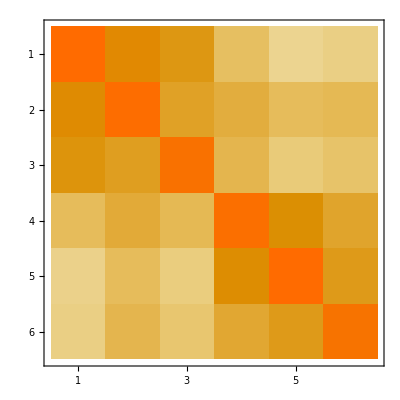

```mathematica
MatrixPlot[Abs@Zmat ]
```

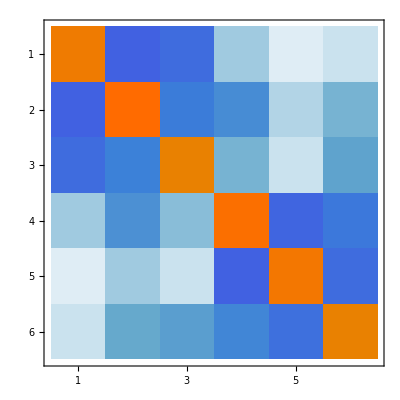

```mathematica
MatrixPlot[Im@Ymat ]
```

```mathematica
a= Exp[I 120 Degree];
A={{1,1,1},{1,a^2,a},{1,a,a^2}};
MatrixForm[A]
```

(1 | 1 | 1
1 | ⅇ^(240 ⅈ °) | ⅇ^(120 ⅈ °)
1 | ⅇ^(120 ⅈ °) | ⅇ^(240 ⅈ °))

```mathematica
(*
ℓ= 80.0;
Y1= 1/(Zpos ℓ) + Ypos ℓ;
Y2= -1/(Zpos ℓ);
 ZL= 376.32086209393407;
Y3= 1/ZL;
*)
```

```mathematica
Ztotal= Zmat 1000 30.0;
Yl=DiagonalMatrix[{1/200, 1/200, 1/200, 0.,0.,0.}];
A=IdentityMatrix[6];
B= Ztotal;
c = 0 A;
```

```mathematica
Q= ArrayFlatten[{{A, B},{c, A}}];
MatrixForm[Q]
```

(1 | 0 | 0 | 0 | 0 | 0 | 3.10525+19.9509 ⅈ | 2.67693+11.9005 ⅈ | 2.759+11.4278 ⅈ | 2.67451+9.98809 ⅈ | 2.63987+9.21505 ⅈ | 2.75168+9.26985 ⅈ
0 | 1 | 0 | 0 | 0 | 0 | 2.67693+11.9005 ⅈ | 3.17267+19.8861 ⅈ | 2.79538+11.2924 ⅈ | 2.7105+11.2169 ⅈ | 2.67451+9.98809 ⅈ | 2.79143+10.011 ⅈ
0 | 0 | 1 | 0 | 0 | 0 | 2.759+11.4278 ⅈ | 2.79538+11.2924 ⅈ | 3.352+19.7281 ⅈ | 2.79143+10.011 ⅈ | 2.75168+9.26985 ⅈ | 2.87711+9.67461 ⅈ
0 | 0 | 0 | 1 | 0 | 0 | 2.67451+9.98809 ⅈ | 2.7105+11.2169 ⅈ | 2.79143+10.011 ⅈ | 3.17267+19.8861 ⅈ | 2.67693+11.9005 ⅈ | 2.79538+11.2924 ⅈ
0 | 0 | 0 | 0 | 1 | 0 | 2.63987+9.21505 ⅈ | 2.67451+9.98809 ⅈ | 2.75168+9.26985 ⅈ | 2.67693+11.9005 ⅈ | 3.10525+19.9509 ⅈ | 2.759+11.4278 ⅈ
0 | 0 | 0 | 0 | 0 | 1 | 2.75168+9.26985 ⅈ | 2.79143+10.011 ⅈ | 2.87711+9.67461 ⅈ | 2.79538+11.2924 ⅈ | 2.759+11.4278 ⅈ | 3.352+19.7281 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

```mathematica
Va= 230./Sqrt[3];
Vb= Va Exp[I 120 Degree];
Vc= Va Exp[-I 120 Degree];
Ia1=Va1/200.;
Ib1= Vb1/200.;
Ic1 = Vc1/200.;
V0={Va, Vb, Vc, Va, Vb, Vc};
I0={Ia, Ib, Ic, 0,0,0};
V1={Va1,Vb1,Vc1,Vd1,Ve1,Vf1};
I1={Ia1,Ib1,Ic1,0,0,0};
```

```mathematica
recv=Join[V1,I1];
```

```mathematica
Q.recv
```

{(0.+0. ⅈ)+(1.01553+0.0997547 ⅈ) Va1+(0.0133847+0.0595026 ⅈ) Vb1+(0.013795+0.0571391 ⅈ) Vc1,(0.+0. ⅈ)+(0.0133847+0.0595026 ⅈ) Va1+(1.01586+0.0994304 ⅈ) Vb1+(0.0139769+0.0564618 ⅈ) Vc1,(0.+0. ⅈ)+(0.013795+0.0571391 ⅈ) Va1+(0.0139769+0.0564618 ⅈ) Vb1+(1.01676+0.0986405 ⅈ) Vc1,(0.+0. ⅈ)+(0.0133726+0.0499405 ⅈ) Va1+(0.0135525+0.0560846 ⅈ) Vb1+(0.0139572+0.050055 ⅈ) Vc1+Vd1,(0.+0. ⅈ)+(0.0131993+0.0460753 ⅈ) Va1+(0.0133726+0.0499405 ⅈ) Vb1+(0.0137584+0.0463492 ⅈ) Vc1+Ve1,(0.+0. ⅈ)+(0.0137584+0.0463492 ⅈ) Va1+(0.0139572+0.050055 ⅈ) Vb1+(0.0143855+0.048373 ⅈ) Vc1+Vf1,0.+0.005 Va1,0.+0.005 Vb1,0.+0.005 Vc1,0.,0.,0.}

```mathematica
Dimensions[%]
```

{12}

```mathematica
snd=Join[V0, I0]
```

{132.791,-66.3953+115. ⅈ,-66.3953-115. ⅈ,132.791,-66.3953+115. ⅈ,-66.3953-115. ⅈ,Ia,Ib,Ic,0,0,0}

```mathematica
Dimensions[%]
```

{12}

```mathematica
sol=Solve[snd==Q.recv,{ Vd,Ve,Vf,Ia,Ib,Ic,Va1,Vb1,Vc1, Vd1,Ve1,Vf1}]
```

{{Ia→0.662784-0.0273361 ⅈ,Ib→-0.306069+0.584916 ⅈ,Ic→-0.35458-0.559042 ⅈ,Va1→132.557-5.46722 ⅈ,Vb1→-61.2138+116.983 ⅈ,Vc1→-70.9159-111.808 ⅈ,Vd1→133.529+0.411117 ⅈ,Ve1→-65.9426+115.282 ⅈ,Vf1→-66.1508-114.599 ⅈ}}

```mathematica
var={Ia,Ib,Ic,Va1,Vb1,Vc1,Vd1,Ve1,Vf1};
```

```mathematica
sol1=var/.Flatten[sol]
```

{0.662784-0.0273361 ⅈ,-0.306069+0.584916 ⅈ,-0.35458-0.559042 ⅈ,132.557-5.46722 ⅈ,-61.2138+116.983 ⅈ,-70.9159-111.808 ⅈ,133.529+0.411117 ⅈ,-65.9426+115.282 ⅈ,-66.1508-114.599 ⅈ}

```mathematica
Abs[sol1]
```

{0.663348,0.660155,0.662008,132.67,132.031,132.402,133.529,132.81,132.321}

```mathematica
Arg[sol1]/π 180
```

{-2.36179,117.622,-122.385,-2.36179,117.622,-122.385,0.176406,119.77,-119.995}

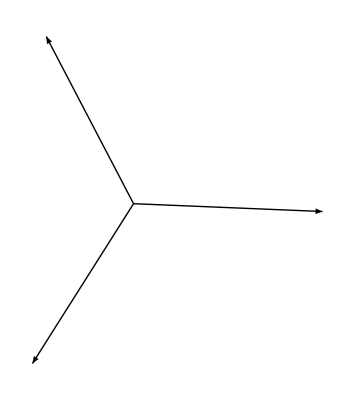

```mathematica
Graphics[{Arrow[{{0,0},{ Re[sol1[[1]]],Im[sol1[[1]]]}}],Arrow[{{0,0},{ Re[sol1[[2]]],Im[sol1[[2]]]}}],Arrow[{{0,0},{ Re[sol1[[3]]],Im[sol1[[3]]]}}]}]
```